From: http://www.nutristrategy.com/caloriesburnedcycling.htm

```mathematica
x={177,325,413,620,738};
```

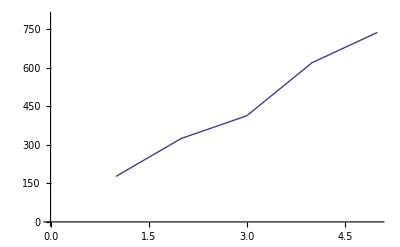

```mathematica
ListLinePlot[x,PlotRange->{{0,5},{0,800}}]
```

It should be taken with grain of salt because according to this:

http://www.crankcycling.com/measuring-energy-expenditure-on-the-bike-continued/

“Riders frequently ask me if their body weight makes a difference, and the answer is no.    A larger rider can typically put out more watts, and therefore  do more kilojoules in a given amount of time.    But is still takes a 100lb rider just as many calories to do 150 watts for an hour,as it takes a 200lb rider to do 150 watts for an hour.  The only difference is that the larger rider will burn more calories as part of his basal metabolic rate, but he would burn those even if he were sitting at his desk typing on his keyboard, so that doesn’t really count towards his energy expenditure from exercise.”

Assuming linear. Data points for “very light” and “very vigorous”.

```mathematica
rpms = {70,100};
cals = {177, 738};
```

```mathematica
data=Transpose[{rpms,cals}]
```

{{70,177},{100,738}}

```mathematica
line=Fit[data,{1,r},r]
```

-1132.+18.7 r

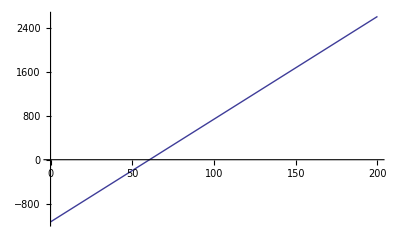

```mathematica
Plot[line,{r,0,200}]
```